```mathematica
SetDirectory[NotebookDirectory[]]
```

SetDirectory[$Failed]

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File object.

```mathematica
Get["library/FeynCalc.m"]
```

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_], LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

```mathematica
FCSetDiracGammaScheme["BMHV"]
```

BMHV

```mathematica
$Assumptions={d>0,e>0,m>0,v>0,u>0,Λ>μ>0}
```

{d>0,e>0,m>0,v>0,u>0,Λ>μ>0}

## d dimensional momentum integral

```mathematica
Ω[d_]:=(2 π^(d/2))/Gamma[d/2]
```

```mathematica
Ω[d]/(2π)^d Integrate[q^(d-1)q^n/((q^2+X)^l),{q,0,∞},Assumptions->{X>0,Y>0,{l,n,d}∈Reals,0≤l≤ 2n}]
```

ConditionalExpression[(2^-d π^(-d/2) X^(3+d/2-l) Gamma[3+d/2] Gamma[-3-d/2+l])/(Gamma[d/2] Gamma[l]), l>0&&6+d<2 l]

```mathematica
ifunc[X_,d_,n_,l_]:=(2^-d π^(-d/2) X^(1/2 (d-2 l+n)) Gamma[-d/2+l-n/2] Gamma[(d+n)/2])/(Gamma[d/2] Gamma[l])
```

```mathematica
FVd[d_,q_,i_]:=Pair[LorentzIndex[i,d],Momentum[q,d]]
```

```mathematica
MTd[d_,i_,j_]:=Pair[LorentzIndex[i,d],LorentzIndex[j,d]]
```

```mathematica
wick[d_,indices_,P_]:=Module[{l=Length[indices],intindices,i,ix,f,g,J1,J2,J3},intindices=Table[ix[i],{i,1,l}];f[s_]:=MTd[d,s[[1]],s[[2]]] Signature[s]^P;g[S_]:=Apply[Times,Map[f,Partition[S,2]]];J1=Map[g,Select[Permutations[intindices],Signature[#]==1&]];J2=Map[g,Select[Permutations[intindices],Signature[#]==-1&]];
J3=1/((l/2)!2^(l/2))(Total[J1]+(-1)^P Total[J2])//FullSimplify;J3//.Thread[intindices-> indices]]
```

```mathematica
intcont[d_,q_,indices_]:=Module[{l=Length[indices],norm},norm=1/(Pochhammer[d/2,l/2] 2^(l/2));If[EvenQ[l],norm Pair[Momentum[q,d],Momentum[q,d]]^(l/2)wick[d,indices,0],0]//FullSimplify]
```

```mathematica
LCdC[d_,i_,j_,k_,l_,m_,n_]:=MTd[d,i,l].(MTd[d,j,m].MTd[d,k,n]-MTd[d,j,n].MTd[d,k,m])-MTd[d,i,m].(MTd[d,j,l].MTd[d,k,n]-MTd[d,j,n].MTd[d,k,l])+MTd[d,i,n].(MTd[d,j,l].MTd[d,k,m]-MTd[d,j,m].MTd[d,k,l])
```

```mathematica
SPd[d_,p_,q_]:=Pair[Momentum[p,d],Momentum[q,d]]
```

```mathematica
dband[d_,q_,L_]:=Module[{i,j},√(d/(2(d-1)))GSD[L[i,j]].FVd[d,q,i].FVd[d,q,j]]
```

```mathematica
G[d_,w_,q_,L_]:=(-I (w)+dband[d,q,L]/(2m))/(( w)^2+(SPd[d,q,q]/(2m))^2)
```

```mathematica
D0[d_,w_,q_]:=(v^2 SPd[d,q,q])/(w^2+v^2 SPd[d,q,q]^2)
```

```mathematica
D1[d_,w_,q_,i_,j_]:=MTd[d,i,j]/(w^2+v^2 SPd[d,q,q]^2)
```

```mathematica
Sigma[a_,b_]:=1/(2I)(GAD[a].GAD[b]-GAD[b].GAD[a])
```

```mathematica
C0=-I e ;
```

```mathematica
C1[d_,q_,L_,i_]:=Module[{j},-e (√(d/(2(d-1)))(GSD[L[i,j]].FVd[d,q,j])/(2m))]
```

```mathematica
AC[d_,m_,n_,r_,s_,j_,k_]:=12I((MTd[d,m,r].(MTd[d,n,j].MTd[d,s,k]-MTd[d,s,j].MTd[d,n,k])+MTd[d,m,s].(MTd[d,n,j].MTd[d,r,k]-MTd[d,r,j].MTd[d,n,k]))+(MTd[d,n,r].(MTd[d,m,j].MTd[d,s,k]-MTd[d,s,j].MTd[d,m,k])+MTd[d,n,s].(MTd[d,m,j].MTd[d,r,k]-MTd[d,r,j].MTd[d,m,k])))
```

```mathematica
AC[d,1,2,3,2,3,1]/.{Pair[ExplicitLorentzIndex[i_],ExplicitLorentzIndex[j_]]-> KroneckerDelta[i,j]}//TraditionalForm
```

12 ⅈ (0.0+0.(0.0-0.1)+0.(0.0-1.0)+1.(0.0-1.1))

```mathematica
AC[d,1,3,1,1,3,1]/.{Pair[ExplicitLorentzIndex[i_],ExplicitLorentzIndex[j_]]-> KroneckerDelta[i,j]}//TraditionalForm
```

12 ⅈ (2 0.0+2 1.(1.1-0.0))

```mathematica
C2[d_,q_,L_,i_]:=Module[{a,b,m,n,r,s,j},-κ Sigma[a,b].(1/(32d(d-2)I)AC[d,m,n,r,s,j,i]).(Pair[LorentzIndex[a,D],Momentum[L[m,n],D]].Pair[LorentzIndex[b,D],Momentum[L[r,s],D]]).(-I FVd[d,q,j])]
```

```mathematica
CubeAniso[d_,q_,arr_,t_,u_,k_,m_]:=-Pair[LorentzIndex[k,d],Momentum[q,d]] .Pair[LorentzIndex[m,d],Momentum[q,d]] .Pair[LorentzIndex[t,d],LorentzIndex[u,d]] .arr[q,{t,u}]+Pair[LorentzIndex[k,d],LorentzIndex[u,d]] .Pair[LorentzIndex[m,d],Momentum[q,d]] .Pair[LorentzIndex[t,d],Momentum[q,d]] .arr[q,{t,u}]+Pair[LorentzIndex[k,d],Momentum[q,d]]. Pair[LorentzIndex[m,d],LorentzIndex[t,d]] .Pair[LorentzIndex[u,d],Momentum[q,d]] .arr[q,{t,u}]-Pair[LorentzIndex[k,d],LorentzIndex[m,d]] .Pair[LorentzIndex[t,d],Momentum[q,d]] .Pair[LorentzIndex[u,d],Momentum[q,d]] .arr[q,{t,u}]-Pair[LorentzIndex[k,d],LorentzIndex[u,d]] .Pair[LorentzIndex[m,d],LorentzIndex[t,d]] .Pair[Momentum[q,d],Momentum[q,d]] .arr[q,{t,u}]+Pair[LorentzIndex[k,d],LorentzIndex[m,d]] .Pair[LorentzIndex[t,d],LorentzIndex[u,d]]. Pair[Momentum[q,d],Momentum[q,d]]. arr[q,{t,u}]
```

```mathematica
LFC[d_,OBX_,L_,LP_,dfunc_,extGammaInd_]:=Module[{A,B,x,i,j,k,l,p,RuleDfunc,RuleDfunc2,Lfunc,finrule},A=OBX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k].MTd[d,j,l]+MTd[d,i,l].MTd[d,j,k]-2/d MTd[d,i,j].MTd[d,k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k].MTd[d,j,l]+MTd[d,i,l].MTd[d,j,k]+2/d MTd[d,i,j].MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k].MTd[d,j,l]+MTd[d,i,l].MTd[d,j,k]+2/d MTd[d,i,j].MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k].MTd[d,j,l]+MTd[d,i,l].MTd[d,j,k]-2/d MTd[d,i,j].MTd[d,k,l]};
B=A//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]],L[i_,i_]:> 0,L[i_,j_]:> Lfunc[LorentzIndex[i,d],LorentzIndex[j,d]]};
RuleDfunc[t_]:= Pair[LorentzIndex[t,D],Momentum[Lfunc[Momentum[p_,d],Momentum[p_,d]],D]]:>1/(√(d/(2(d-1))))FVD[dfunc[p],t];
RuleDfunc2[t_]:= Lfunc[LorentzIndex[i_,d],LorentzIndex[i_,d]]:>0;
finrule=Join[Table[RuleDfunc[t],{t,extGammaInd}],Table[RuleDfunc2[t],{t,extGammaInd}]];
FullSimplify[ScalarProductExpand[Contract[B]]//.finrule]]
```

```mathematica
LoopEvaluate[d_,pwr_,OBX_,w_,q_,arr_,L_,LP_,dfunc_,p0_,p_,extInd_,extGammaInd_]:=Module[{AX,BX,BX1,BX2,FreqPoles,PosPolePos,FreqPosPoles,ResX,CX,CX1,DX,EX,FX,FX1,CFX,GX,GX1,HX,IX,JX,LX,KX,MX,NX,PX,QX,indexP,denomPW,feynprefact,TabTot,TabS,A,B,PreFactX,X,Y,x,y,z,i,j,k,l,eta,lmax,n,s,s1,s2,arrsplit,arrjoin,a,b,c,a1,a2,a3,a4,b1,b2,b3,b4,c1,c2,c3,c4,d1,d2,d3,d4,t,u,t1,t2,t3,t4,Lfunc,NewRule,RuleFunc,NewDRule,Rulefunc2,RuleDfunc,RuleDfunc2,RuleDfunc3,feynintdom,C1,qFX,qFNORM},
(*AX=1/(2π)Integrate[OBX,w];
BX=Limit[AX,w-> ∞]-Limit[AX,w-> -∞];BX1=BX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]-2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]+2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]+2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]-2/d MTd[d,i,j]MTd[d,k,l]};
CX= Contract[ExpandAll2[BX1//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]]}]];*)
BX1=OBX//.{w->  z};
BX2=Denominator[BX1];
ResX[x_]:=Residue[BX1,{z,x}];
FreqPoles=z/.Solve[BX2==0,z];PosPolePos=FullSimplify[HeavisideTheta[Im[ExpandScalarProduct[FreqPoles]//.{p0-> 0,Momentum[p,d]->0}]],Pair[Momentum[q,d],Momentum[q,d]]>0];
CX=I Map[ResX,FreqPoles].PosPolePos;
AX=CX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k].MTd[d,j,l]+MTd[d,i,l].MTd[d,j,k]-2/d MTd[d,i,j].MTd[d,k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k].MTd[d,j,l]+MTd[d,i,l].MTd[d,j,k]+2/d MTd[d,i,j].MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k].MTd[d,j,l]+MTd[d,i,l].MTd[d,j,k]+2/d MTd[d,i,j].MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k].MTd[d,j,l]+MTd[d,i,l].MTd[d,j,k]-2/d MTd[d,i,j].MTd[d,k,l]};
BX= Contract[ExpandAll2[AX//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_:>  Pair[LorentzIndex[i,d],LorentzIndex[j,d]]}]];
DX=ExpandScalarProduct[BX]/.{p0->s^2 p0,Momentum[p,d]-> s Momentum[p,d]};
FX=SeriesCoefficient[DX,{s,0,pwr}];RuleFunc[t_]:=Pair[LorentzIndex[t,d],Momentum[p,d]]:> arr[p,{t}];
Rulefunc2[x_,y_,l_]:=arr[p,Table[a[i],{i,1,l}]]arr[q,Table[a[i],{i,1,l}]];
NewRule=Join[{Pair[LorentzIndex[t_,d],Momentum[q,d]]:> arr[q,{t}],Pair[Momentum[p,d],Momentum[q,d]]:> arr[p,{a1}]arr[q,{a1}],Pair[Momentum[p,d],Momentum[q,d]]^l_:> Rulefunc2[p,q,l]},Table[RuleFunc[t],{t,extInd}]];
JX=ExpandAll2[FX]//.NewRule;
arrsplit[x_,s_]:=Apply[Times,Table[FVd[d,x,i],{i,s}]];
arrjoin[x_,s_,l_]:=arr[x,Flatten[Table[s,{i,1,l}]]];
KX=JX//.{arr[q,s1_]arr[q,s2_]-> arr[q,Join[s1,s2]],arr[q,s_]^l_:> arrjoin[q,s,l],arr[p,s1_]arr[p,s2_]-> arr[p,Join[s1,s2]],arr[p,s_]^l_:> arrjoin[p,s,l]};
LX=KX//.{arr[q,s_]:> intcont[d,q,s]};
MX=LX//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]],L[i_,i_]:> 0,L[i_,j_]:> Lfunc[LorentzIndex[i,d],LorentzIndex[j,d]],arr[p,s_]:> arrsplit[p,s]};
RuleDfunc[t_]:= Pair[LorentzIndex[t,D],Momentum[Lfunc[Momentum[p,d],Momentum[p,d]],D]]:>1/(√(d/(2(d-1))))FVD[dfunc[p],t];
RuleDfunc2[t_]:= Lfunc[LorentzIndex[i_,d],LorentzIndex[i_,d]]:>0;
NewDRule=Join[Table[RuleDfunc[t],{t,extGammaInd}],Table[RuleDfunc2[t],{t,extGammaInd}]];
(*FullSimplify[Contract[MX]//.NewDRule]*)
FullSimplify[Coefficient[Contract[MX]//.NewDRule,Pair[Momentum[q,d],Momentum[q,d]],-2],Pair[Momentum[q,d],Momentum[q,d]]>0](-Log[μ/Λ]/(8 π^2))]
```

```mathematica
Ω[4]/(2π)^4 Integrate[1/q,{q,μ,Λ},Assumptions->{r>0}]
```

(Log[Λ]-Log[μ])/(8 π^2)

## Computation in the symmetric limit

## Computation for δZ_1

```mathematica
L1=TR[C1[d,q,L,i].G[d,k0+q0,q,L].C1[d,q,L,j].D1[d,q0,q,i,j],Contract-> False];
L2=TR[C0 .G[d,k0+q0,q,L].C0 .D0[d,q0,q],Contract-> False];
CT=TR[-Subscript[δZ, 1](I k0),Contract-> False];
ExtPwr=2;
LEQ1=FullSimplify[LoopEvaluate[d,ExtPwr,L1,q0,q,arr,L,LP,d,k0,k,{},{}]+LoopEvaluate[d,ExtPwr,L2,q0,q,arr,L,LP,d,k0,k,{},{}]]+LFC[d,CT,L,LP,d,{}];
LEQ1//TraditionalForm
```

(ⅈ e^2 k0 (d-8 m^2 v^2+2) log(μ/Λ))/(8 v (2 π m v+π)^2)-4 ⅈ δZ_1 k0

```mathematica
SOL1=FullSimplify[Solve[LEQ1==0,Subscript[δZ, 1]]];
SOL1//TraditionalForm
```

{{δZ_1→(e^2 (d-8 m^2 v^2+2) log(μ/Λ))/(32 v (2 π m v+π)^2)}}

## Computation for δZ_2

```mathematica
L1=TR[C1[d,q+2k,L,i].G[d,q0+k0,k+q,L].C1[d,q+2k,L,j].D1[d,q0,q,i,j].GAD[a],Contract-> False];
L2=TR[C0. G[d,q0,q,L].C0 .D0[d,q0-k0,q-k].GAD[a],Contract-> False];
CT=TR[(-Subscript[δZ, 2] dband[d,k,L]/(2m)).GAD[a],Contract-> False];
ExtPwr=2;
LEQ2=FullSimplify[LoopEvaluate[d,ExtPwr,L1,q0,q,arr,L,LP,d,k0,k,{},{a}]+LoopEvaluate[d,ExtPwr,L2,q0,q,arr,L,LP,d,k0,k,{},{a}]]+LFC[d,CT,L,LP,d,{a}];
LEQ2//TraditionalForm
```

(e^2 (d(k))^a (((d-2) (d^3+4 (d-1) (d^2-8) m v-3 d^2+4 (d-2) (d+3) d m^2 v^2-2 d+8))/(d-1)+256 m^4 v^4) log(μ/Λ))/(16 π^2 d (d+2) m v (2 m v+1)^3)-(2 δZ_2 (d(k))^a)/m

```mathematica
SOL2=FullSimplify[Normal[Solve[FullSimplify[LEQ2]==0,Subscript[δZ, 2]]]];
SOL2//TraditionalForm
```

{{δZ_2→(e^2 (4 (d-2) (d-1) (d^2-8) m v+256 (d-1) m^4 v^4+4 (d-2)^2 d (d+3) m^2 v^2+(d-2)^2 ((d-1) d-4)) log(μ/Λ))/(32 π^2 (d-1) d (d+2) v (2 m v+1)^3)}}

## Computation for δZ_3

```mathematica
L1=-TR[(C0).G[d,q0,q+k,L].(C0).G[d,q0,q,L],Contract-> False];
CT=-Subscript[δZ, 3]SPd[d,k,k];
ExtPwr=2;
LEQ3=LoopEvaluate[d,ExtPwr,L1,q0,q,arr,L,LP,d,k0,k,{},{}]+LFC[d,CT,L,LP,d,{}];
LEQ3//TraditionalForm
```

(e^2 k^2 m log(μ/Λ))/(4 π^2)-δZ_3 k^2

```mathematica
SOL3=FullSimplify[Solve[LEQ3==0,Subscript[δZ, 3]]];
SOL3//TraditionalForm
```

{{δZ_3→(e^2 m log(μ/Λ))/(4 π^2)}}

## (Spatial) transverse and longitudinal projectors

```mathematica
PT[d_,p_,i_,j_]:=MTd[d,i,j]-(FVd[d,p,i].FVd[d,p,j])/SPd[d,p,p]
```

```mathematica
PL[d_,p_,i_,j_]:=(FVd[d,p,i].FVd[d,p,j])/SPd[d,p,p]
```

```mathematica
L1=-TR[C1[d,2q+k,L,i].G[d,q0,q+k,L].C1[d,2q+k,L,l].G[d,q0,q,L],Contract-> False];
CT=-TR[Subscript[δZ, 4] v^2 SPd[d,k,k]^2 PT[d,k,i,l]] ;
ExtPwr=4;
LEQ4=LoopEvaluate[d,ExtPwr,L1,q0,q,arr,L,LP,d,k0,k,{},{}]+CT;
LEQ4p=Collect2[Contract[LEQ4.PT[d,k,l,j]],Log[μ/Λ],FullSimplify];
Collect[LEQ4p,Subscript[δZ, 4]]//TraditionalForm
```

((d-2) (3 d^3+8 d^2+2 d-8) e^2 k^2 log(μ/Λ) (k^i k^j-k^2 g^ij))/(16 π^2 (d-1)^2 (d+2) (d+4) m)+4 δZ_4 k^2 v^2 (k^i k^j-k^2 g^ij)

## Computation for δZ_4

#### Transverse part of the renormalized vacuum polarization

```mathematica
L1=-TR[C1[d,2q+k,L,i].G[d,q0,q+k,L].C1[d,2q+k,L,l].G[d,q0,q,L],Contract-> False];
CT=-TR[Subscript[δZ, 4] v^2 SPd[d,k,k]^2 PT[d,k,i,l]] ;
ExtPwr=4;
LEQ4=LoopEvaluate[d,ExtPwr,L1,q0,q,arr,L,LP,d,k0,k,{},{}]+CT;
LEQ4p=Collect2[Contract[LEQ4.PT[d,k,l,j]],Log[μ/Λ],FullSimplify];
Collect[LEQ4p,Subscript[δZ, 4]]//TraditionalForm
```

((d-2) (3 d^3+8 d^2+2 d-8) e^2 k^2 log(μ/Λ) (k^i k^j-k^2 g^ij))/(16 π^2 (d-1)^2 (d+2) (d+4) m)+4 δZ_4 k^2 v^2 (k^i k^j-k^2 g^ij)

```mathematica
FullSimplify[TR[LEQ4.PL[d,k,j,l]]]//TraditionalForm
```

((d-4) (d-2) e^2 k^2 k^i k^j log(Λ/μ))/(2 π^2 (d+2) (d+4) m)

```mathematica
SOL4=FullSimplify[Solve[LEQ4p==0,Subscript[δZ, 4]]];
SOL4//TraditionalForm
```

{{δZ_4→((d-2) (d (d (3 d+8)+2)-8) e^2 log(Λ/μ))/(64 π^2 (d-1)^2 (d+2) (d+4) m v^2)}}

## Computation of the gamma and beta functions with g_1=((e^2 m)/(8 π^2))^, g_2= 1/v,g_3=1/m

```mathematica
dZarr={1+Subscript[δZ, 1],1+Subscript[δZ, 2],1+ Subscript[δZ, 3],1+ Subscript[δZ, 4]}/.Flatten[Join[SOL1,SOL2,SOL3,SOL4]];
ZX=FullSimplify[Factor[dZarr//.{e->  √(8 π^2 g1/m) ,v-> 1/g2,m-> 1/g3 }],{d>1}]
```

{1+(g1 g2 g3 (-8+(2+d) g2^2 g3^2) Log[μ/Λ])/(4 (2+g2 g3)^2),1/(4 (-1+d) d (2+d) (2+g2 g3)^3)(4 d (-2+d+d^2) (2+g2 g3)^3+g1 (256 (-1+d)+4 (-2+d)^2 d (3+d) g2^2 g3^2+4 (-2+d) (-1+d) (-8+d^2) g2^3 g3^3+(-2+d)^2 (-4+(-1+d) d) g2^4 g3^4) Log[μ/Λ]),1+2 g1 Log[μ/Λ],1+((-2+d) (-8+d (2+d (8+3 d))) g1 g2^2 g3^2 Log[Λ/μ])/(8 (-1+d)^2 (2+d) (4+d))}

```mathematica
{γ1,γ2,γ3,γ4}=FullSimplify[μ D[ZX,μ]]
```

{(g1 g2 g3 (-8+(2+d) g2^2 g3^2))/(4 (2+g2 g3)^2),(g1 (256 (-1+d)+4 (-2+d)^2 d (3+d) g2^2 g3^2+4 (-2+d) (-1+d) (-8+d^2) g2^3 g3^3+(-2+d)^2 (-4+(-1+d) d) g2^4 g3^4))/(4 (-1+d) d (2+d) (2+g2 g3)^3),2 g1,-((-2+d) (-8+d (2+d (8+3 d))) g1 g2^2 g3^2)/(8 (-1+d)^2 (2+d) (4+d))}

### The renormalization constants at v = ∞

```mathematica
Series[{γ1,γ2,γ3,γ4},{g2,0,0}]
```

{-1/2 (g1 g3) g2+O[g2]^2,(8 g1)/(d (2+d))+O[g2]^1,2 g1,-(((-2+d) (-8+2 d+8 d^2+3 d^3) g1 g3^2) g2^2)/(8 ((-1+d)^2 (2+d) (4+d)))+O[g2]^3}

### The RG flow with 1/m chosen to be marginal by fixing z

```mathematica
ZSOL=Flatten[FullSimplify[Solve[-(z-2+γ2-γ1)==0,z]]]
```

{z→2+1/(2 (-1+d) d (2+d) (2+g2 g3)^3)g1 (-128 (-1+d)-8 (-1+d) d (2+d) g2 g3-2 d (8+d (-6+d+d^2)) g2^2 g3^2-(-1+d) (32+(-10+d) d (2+d)) g2^3 g3^3+2 (4+d (-4+d (-1+2 d))) g2^4 g3^4)}

```mathematica
AX=-(4-d+γ1-γ2-γ3)g1/.ZSOL
```

g1 (-4+d+2 g1-(g1 g2 g3 (-8+(2+d) g2^2 g3^2))/(4 (2+g2 g3)^2)+(g1 (256 (-1+d)+4 (-2+d)^2 d (3+d) g2^2 g3^2+4 (-2+d) (-1+d) (-8+d^2) g2^3 g3^3+(-2+d)^2 (-4+(-1+d) d) g2^4 g3^4))/(4 (-1+d) d (2+d) (2+g2 g3)^3))

```mathematica
BX=-(2-z+(γ3-γ4)/2)g2/.ZSOL
```

g2 (1/2 (-2 g1-((-2+d) (-8+d (2+d (8+3 d))) g1 g2^2 g3^2)/(8 (-1+d)^2 (2+d) (4+d)))+1/(2 (-1+d) d (2+d) (2+g2 g3)^3)g1 (-128 (-1+d)-8 (-1+d) d (2+d) g2 g3-2 d (8+d (-6+d+d^2)) g2^2 g3^2-(-1+d) (32+(-10+d) d (2+d)) g2^3 g3^3+2 (4+d (-4+d (-1+2 d))) g2^4 g3^4))

```mathematica
Beta1[g1_,g2_,g3_,d_]:=g1 (-4+d+2 g1-(g1 g2 g3 (-8+(2+d) g2^2 g3^2))/(4 (2+g2 g3)^2)+(g1 (256 (-1+d)+4 (-2+d)^2 d (3+d) g2^2 g3^2+4 (-2+d) (-1+d) (-8+d^2) g2^3 g3^3+(-2+d)^2 (-4+(-1+d) d) g2^4 g3^4))/(4 (-1+d) d (2+d) (2+g2 g3)^3))
```

```mathematica
Beta2[g1_,g2_,g3_,d_]:=g2 (-2+1/2 (-2 g1-((-2+d) (-8+d (2+d (8+3 d))) g1 g2^2 g3^2)/(8 (-1+d)^2 (2+d) (4+d)))-1/(2 d (-2+d+d^2) (2+g2 g3)^3)(-32 (-1+d) (d (2+d)-4 g1)+8 (-1+d) d (2+d) (-6+g1) g2 g3+2 d (-12 d (1+d)+d (-6+d+d^2) g1+8 (3+g1)) g2^2 g3^2+(-1+d) (32 g1+d (2+d) (-4+(-10+d) g1)) g2^3 g3^3+2 (-4+d (4+d-2 d^2)) g1 g2^4 g3^4))
```

```mathematica
Beta3[g1_,g2_,g3_,d_]:=0
```

### The beta functions and dynamic exponents close to the v = ∞ fixed point

#### Dynamic exponent

```mathematica
FullSimplify[Series[z/.ZSOL,{g2,0,0}]]
```

(2-(8 g1)/(d (2+d)))+O[g2]^1

#### The charge beta function

```mathematica
XBE=FullSimplify[Series[-Beta1[g1,g2,g3,d],{g2,0,0}]]
```

g1 (4-d-2 g1-(8 g1)/(d (2+d)))+O[g2]^1

```mathematica
FullSimplify[Solve[Normal[XBE]==0,g1]]
```

{{g1→0},{g1→-((-4+d) d (2+d))/(8+2 d (2+d))}}

```mathematica
-((-4+d) d (2+d))/(8+2 d (2+d))/.{d-> 3}
```

15/38

#### If you compare with Moon et al., they have z = 2 - 8 u/15. Our g1 is their u. So it matches perfectly. Their critical u^*=15ϵ/(30 N_f+8) ~15ϵ/38 is the same as our estimation. So we have the correct critical point.

#### However, this critical point is not stable for non-zero 1/v

```mathematica
FullSimplify[Series[-Beta1[g1,g2,g3,3],{g2,0,1}]]
```

(g1-(38 g1^2)/15)+3/10 g1^2 g3 g2+O[g2]^2

```mathematica
FullSimplify[Series[-Beta2[g1,g2,g3,3],{g2,0,1}]]
```

(23 g1 g2)/15+O[g2]^2

#### Three dimensional flow

```mathematica
range1=4;
range2=4;
range3=4;
ddim=3;
xsfg=StreamPlot3D[{-Beta1[g1,g2,g3,ddim],-Beta2[g1,g2,g3,ddim],-Beta3[g1,g2,g3,ddim]},{g1,0,range1},{g2,0,range2},{g3,0,range3},StreamMarkers->"Arrow3D",StreamScale->Small,StreamStyle->Red,StreamColorFunction->None,(*Epilog->{Red,PointSize[.04],Point[{x0,y0}]},*)PlotRange-> {{0,range1},{0,range2},{0,range3}},TicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],AxesStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Style["e^2m/8π^2",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black],Style["1/v",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black],Style["1/m",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black]}
(*ImagePadding->{{80,40},{70,10}}*)
]
```

-Graphics3D-

#### Both the flows indicate marginal relevance due to non-zero g2 = 1/v . Let’s look at the flow.

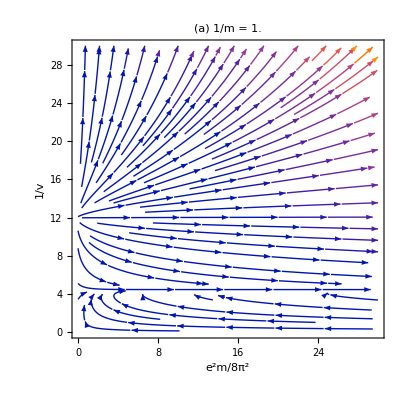

```mathematica
range1=30;
range2=30;
ddim=3;
g3x=1;
xfg=StreamPlot[{-Beta1[g1,g2,g3x,ddim],-Beta2[g1,g2,g3x,ddim]},{g1,0,range1},{g2,0,range2},StreamScale->Large,(*Epilog->{Red,PointSize[.04],Point[{x0,y0}]},*)PlotRange-> {{0,range1},{0,range2}},FrameTicks->{{All,None},{All,None}},FrameTicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],BoundaryStyle->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["e^2m/8π^2",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black],Style["1/v",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black]},
PlotLabel->Style["(a) 1/m = "<>ToString[N[g3x]],FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->20,FontColor->Black],
ImagePadding->{{80,40},{70,10}}
]
```

```mathematica
FullSimplify[Series[-Beta1[g1,g2,g3,3],{g1,∞,1}]]
```

((-608+g2 g3 (-840+g2 g3 (-438+g2 g3 (13+37 g2 g3)))) g1^2)/(30 (2+g2 g3)^3)+g1+O[1/g1]^2

```mathematica
FullSimplify[Series[-Beta2[g1,g2,g3,3],{g1,∞,1}]]
```

(g2 (82432+g2 g3 (107520+g2 g3 (61416+g2 g3 (-4196+g2 g3 (-5570+453 g2 g3))))) g1)/(6720 (2+g2 g3)^3)+O[1/g1]^2

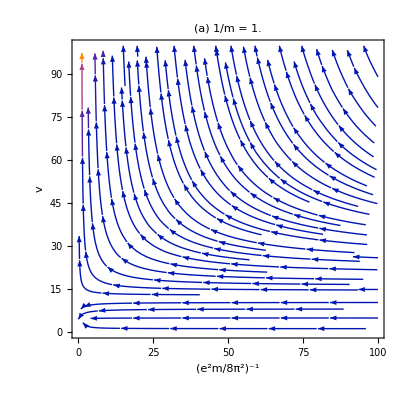

```mathematica
range1=100;
range2=100;
ddim=3;
g3x=1;
xfg=StreamPlot[{-(-Beta1[1/g1,g2,g3x,ddim] g1^2),-Beta2[1/g1,g2,g3x,ddim]},{g1,0,range1},{g2,0,range2},StreamScale->Large,(*Epilog->{Red,PointSize[.04],Point[{x0,y0}]},*)PlotRange-> {{0,range1},{0,range2}},FrameTicks->{{All,None},{All,None}},FrameTicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],BoundaryStyle->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["(e^2m/8π^2)^-1",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black],Style["v",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black]},
PlotLabel->Style["(a) 1/m = "<>ToString[N[g3x]],FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->20,FontColor->Black],
ImagePadding->{{80,40},{70,10}}
]
```

## To study the flow we shall compute the gamma and beta functions with a different parametrization - g_1=((e^2 m)/(8 π^2))^, g_2= e^2/(8 π^2 v)

```mathematica
dZarr={1+Subscript[δZ, 1],1+Subscript[δZ, 2],1+ Subscript[δZ, 3],1+ Subscript[δZ, 4]}/.Flatten[Join[SOL1,SOL2,SOL3,SOL4]];
ZX=FullSimplify[Factor[dZarr//.{m-> 8 π^2 g1/e^2,e-> √(8 π^2 g2 v) }],{d>1}]
```

{1+(g2 (-8 g1^2+(2+d) g2^2) Log[μ/Λ])/(4 (2 g1+g2)^2),1/(4 (-1+d) d (2+d) (2 g1+g2)^3)(4 d (-2+d+d^2) (2 g1+g2)^3+(256 (-1+d) g1^4+4 (-2+d)^2 d (3+d) g1^2 g2^2+4 (-2+d) (-1+d) (-8+d^2) g1 g2^3+(-2+d)^2 (-4+(-1+d) d) g2^4) Log[μ/Λ]),1+2 g1 Log[μ/Λ],1+((-2+d) (-8+d (2+d (8+3 d))) g2^2 Log[Λ/μ])/(8 (-1+d)^2 (2+d) (4+d) g1)}

```mathematica
{γ1,γ2,γ3,γ4}=FullSimplify[μ D[ZX,μ]]
```

{(g2 (-8 g1^2+(2+d) g2^2))/(4 (2 g1+g2)^2),(256 (-1+d) g1^4+4 (-2+d)^2 d (3+d) g1^2 g2^2+4 (-2+d) (-1+d) (-8+d^2) g1 g2^3+(-2+d)^2 (-4+(-1+d) d) g2^4)/(4 (-1+d) d (2+d) (2 g1+g2)^3),2 g1,-((-2+d) (-8+d (2+d (8+3 d))) g2^2)/(8 (-1+d)^2 (2+d) (4+d) g1)}

### The RG flow from Counter terms

```mathematica
AX=-(4-d+γ1-γ2-γ3)g1
```

g1 (-4+d+2 g1-(g2 (-8 g1^2+(2+d) g2^2))/(4 (2 g1+g2)^2)+(256 (-1+d) g1^4+4 (-2+d)^2 d (3+d) g1^2 g2^2+4 (-2+d) (-1+d) (-8+d^2) g1 g2^3+(-2+d)^2 (-4+(-1+d) d) g2^4)/(4 (-1+d) d (2+d) (2 g1+g2)^3))

```mathematica
BX=-(4-d+(γ3-γ4)/2-γ3)g2
```

g2 (-4+d+2 g1+1/2 (-2 g1-((-2+d) (-8+d (2+d (8+3 d))) g2^2)/(8 (-1+d)^2 (2+d) (4+d) g1)))

```mathematica
Beta1[g1_,g2_,d_]:=g1 (-4+d+2 g1-(g2 (-8 g1^2+(2+d) g2^2))/(4 (2 g1+g2)^2)+(256 (-1+d) g1^4+4 (-2+d)^2 d (3+d) g1^2 g2^2+4 (-2+d) (-1+d) (-8+d^2) g1 g2^3+(-2+d)^2 (-4+(-1+d) d) g2^4)/(4 (-1+d) d (2+d) (2 g1+g2)^3))
```

```mathematica
Beta2[g1_,g2_,d_]:=g2 (-4+d+2 g1+1/2 (-2 g1-((-2+d) (-8+d (2+d (8+3 d))) g2^2)/(8 (-1+d)^2 (2+d) (4+d) g1)))
```

```mathematica
Series[-Beta1[g1,g2,3],{g2,∞,1}]
```

(37 g1 g2)/30+(1-(209 g1)/30) g1+(62 g1^3)/(5 g2)+O[1/g2]^2

```mathematica
Series[-Beta2[g1,g2,3],{g2,∞,1}]
```

(151 g2^3)/(2240 g1)+(1-g1) g2+O[1/g2]^2

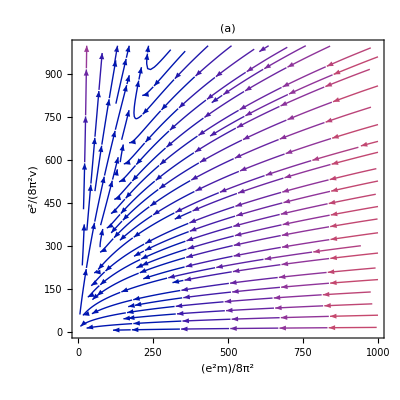

```mathematica
range1=1000;
range2=1000;
ddim=3;
xfg=StreamPlot[{-Beta1[g1,g2,ddim],-Beta2[g1,g2,ddim]},{g1,0,range1},{g2,0,range2},StreamScale->Large,(*Epilog->{Red,PointSize[.04],Point[{x0,y0}]},*)PlotRange-> {{0,range1},{0,range2}},FrameTicks->{{All,None},{All,None}},FrameTicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],BoundaryStyle->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["(e^2m)/8π^2",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black],Style["e^2/(8π^2v)",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->20,FontColor->Black]},
PlotLabel->Style["(a)",FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->20,FontColor->Black],
ImagePadding->{{80,40},{70,10}}
]
```

## Insertion of the relevant u^2/4 F_ij^2 term

```mathematica
GFM[d_,w_,q_,i_,j_]:=u^2/2 SPd[d,q,q].PT[d,q,i,j]
```

## Computation for δZ_11

```mathematica
L1=TR[C1[d,q+2k,L,i].G[d,k0+q0,q+k,L].C1[d,q+2k,L,j].D1[d,q0,q,i,l].GFM[d,q0,q,l,m].D1[d,q0,q,m,j],Contract-> False];
CT=TR[-Subscript[δZ, 11](I k0),Contract-> False];
LEQ11=FullSimplify[LoopEvaluate[d,2,L1,q0,q,arr,L,LP,d,k0,k,{},{}]]+LFC[d,CT,L,LP,d,{}];
LEQ11//TraditionalForm
```

-4 ⅈ δZ_11 k0

```mathematica
SOL11=FullSimplify[Solve[LEQ11==0,Subscript[δZ, 11]]];
SOL11//TraditionalForm
```

{{δZ_11→0}}

## Computation for δZ_12

```mathematica
L1=TR[C1[d,q+2k,L,i].G[d,q0+k0,k+q,L].C1[d,q+2k,L,j].D1[d,q0,q,i,l].GFM[d,q0,q,l,m].D1[d,q0,q,m,j].GAD[a],Contract-> False];
CT=TR[(-Subscript[δZ, 12] dband[d,k,L]/(2m)).GAD[a],Contract-> False];
LEQ12=FullSimplify[LoopEvaluate[d,2,L1,q0,q,arr,L,LP,d,k0,k,{},{a}]]+LFC[d,CT,L,LP,d,{a}];
LEQ12//TraditionalForm
```

-(2 δZ_12 (d(k))^a)/m

```mathematica
SOL12=FullSimplify[Normal[Solve[FullSimplify[LEQ12]==0,Subscript[δZ, 12]]]];
SOL12//TraditionalForm
```

{{δZ_12→0}}

## Computation for δZ_02

```mathematica
L1=TR[C1[d,q+2k,L,i].G[d,q0+k0,k+q,L].C1[d,q+2k,L,j].D1[d,q0,q,i,l].GFM[d,q0,q,l,m].D1[d,q0,q,m,j],Contract-> False];
CT=TR[(-Subscript[δZ, 20] ρ^2),Contract-> False];
LEQ12=FullSimplify[LoopEvaluate[d,0,L1,q0,q,arr,L,LP,d,k0,k,{},{a}]]+LFC[d,CT,L,LP,d,{}];
LEQ12//TraditionalForm
```

(d e^2 m^2 u^2 log(μ/Λ))/(4 π^2 (1-4 m^2 v^2)^2)-4 δZ_20 ρ^2

### A mass is being generated!